Programa que calcula los pares de los motores de un manipulador RR

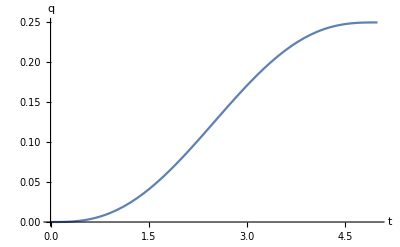

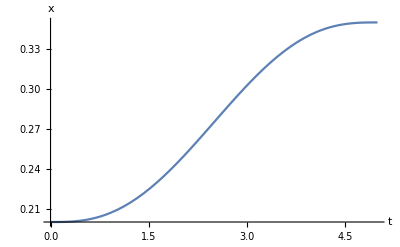

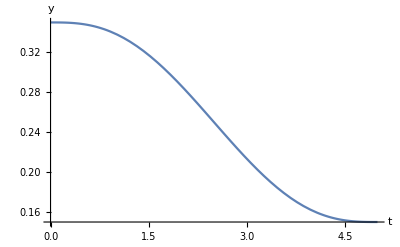

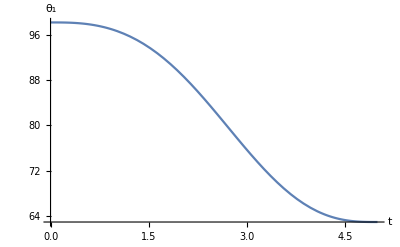

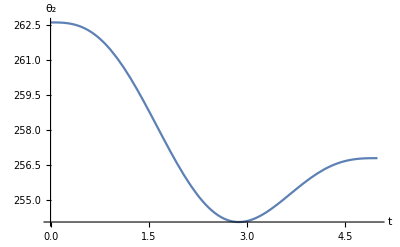

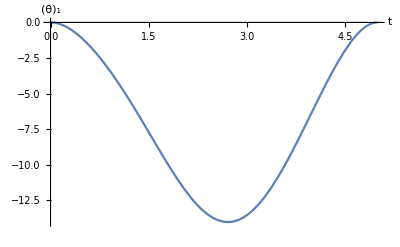

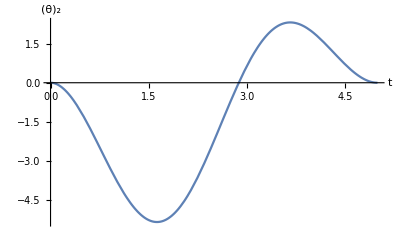

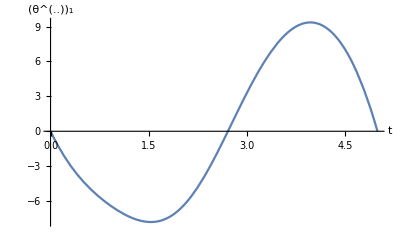

```mathematica
(* Datos del brazo *)
(* masa en [kg] *)
m[1]=1.5;
m[2]=1;
(* Longitudes de los eslabones [m] *)
l1=.35;
l2=.25;
(* Aceleración de la gravedad *)
g=-9.81;
(* coordenadas de la recta *)
P0={.20,.35,0};
Pf={.35,.15,0};


(* Se extraen sólos las coordenadas en x y y de cada punto inicial y final *)

linea=Line[{100*P0[[1;;2]],100*Pf[[1;;2]]}];
(* Multiplicar por 100 para manejo en [cm] con fines de visualización *)
(* Opciones para hacer más sencilla la visualización *)
ejes=Axes->True;
rango=PlotRange->{{-30,50},{-30,50}};
letreros=AxesLabel->{"x","y"};
aspecto=AspectRatio->1/1;
origen=AxesOrigin->{0,0};

(* Línea que describirá el OT, gruesa y amarilla *)
recta={Thick,Pink,linea};


(* Definiendo el generador de trayectoria *)
qf=√((Pf[[1]]-P0[[1]])^2+(Pf[[2]]-P0[[2]])^2+(Pf[[3]]-P0[[3]])^2);
tf=5;
(* Descripción del perfil quíntico *)
q=qf(10(t/tf)^3-15(t/tf)^4+6(t/tf)^5);
(* Parametrizando la recta *)
x=P0[[1]]+q/qf(Pf[[1]]-P0[[1]]);
y=P0[[2]]+q/qf(Pf[[2]]-P0[[2]]);
z=P0[[3]]+q/qf(Pf[[3]]-P0[[3]]);
(* Modelado inverso *)
l3=√(x^2+y^2);
θ[1]=ArcTan[x,y]+ArcTan[l1^2+l3^2-l2^2,√(4 l1^2 l3^2-(l1^2+l3^2-l2^2)^2)];
θ[2]=π+ArcTan[l1^2+l2^2-l3^2,√(4 l1^2 l2^2-(l1^2+l2^2-l3^2)^2)];
(* Derivadas articulares *)
θp[1]=D[θ[1],t];
θp[2]=D[θ[2],t];
θpp[1]=D[θp[1],t];
θpp[2]=D[θp[2],t];
(* Gráficas del perfil, y de la posición *)
Plot[q,{t,0,tf},AxesLabel->{"t","q"}]
Plot[x,{t,0,tf},AxesLabel->{"t","x"}]
Plot[y,{t,0,tf},AxesLabel->{"t","y"}]
(* Gráficas de las variables articulares *)
Plot[θ[1](180/π),{t,0,tf},AxesLabel->{"t","θ_1"}]
Plot[θ[2](180/π),{t,0,tf},AxesLabel->{"t","θ_2"}]

Plot[θp[1](180/π),{t,0,tf},AxesLabel->{"t","(θ̇)_1"}]
Plot[θp[2](180/π),{t,0,tf},AxesLabel->{"t","(θ̇)_2"}]


Plot[θpp[1](180/π),{t,0,tf},AxesLabel->{"t","(θ^(..))_1"}]
Plot[θpp[2](180/π),{t,0,tf},AxesLabel->{"t","(θ^(..))_2"}]

(* Composición del manipulador *)

J1={0,0,0};
JI={100*l1 Cos[θ[1]],100*l1 Sin[θ[1]],0};
JF={100*x,100*y,100*z};

(* Generando eslabones del brazo, extrayendo sólo las primeras dos coordenadas *)
robot=Line[{J1[[1;;2]],JI[[1;;2]],JF[[1;;2]]}];

(* Dibujando el manipulador con línea gruesa roja *)
manipulador={Thick,Red,robot};
imagen=Graphics[{recta,manipulador},ejes,rango,letreros,aspecto,origen];

Tabla=Table[imagen,{t,0,tf,.1}];
ListAnimate[Tabla]

(* Evaluación del par de los motores *)

motor1=1.5*(1/6 (-3 g l1 Cos[θ[1]] m[1]+2 l1^2 m[1] θpp[1]+l2 m[2] (3 g Cos[θ[1]+θ[2]]+2 l2 θpp[1]-l2 θpp[2])));
motor2=1.5*(-1/6 l2 m[2] (3 g Cos[θ[1]+θ[2]]+l2 (θpp[1]-2 θpp[2])));
Plot[motor1,{t,0,tf},AxesLabel->{"t","motor1"}]
Plot[motor2,{t,0,tf},AxesLabel->{"t","motor2"}]
```